# Simplified ADAF spectrum

## Based on Mahadevan, ApJ, 1997, 477, 585.

Notebook adapted from a Maple code that I wrote for my master's dissertation on the period 2003-2005. For the original version, check the Maple worksheet adafMahadevanAdvElet.mws.

Other ideas for improving the code:

Include advection by electrons. In the previous Maple version I was calculating incorrectly the electron advection term.

Incorporate mass-loss due to outflows in the accretion flow (a la Blandford & Begelman 1999): new parameter p. The problem with this is that I would have to recalculate several quantities to get the SED and this would take more time than I have. Given the δ/p degeneracy (see Quataert et al. 1999) I won't do this.

Inner radius of the ADAF (the innermost stable circular orbit) is coupled to black hole spin: the spin j should be a new parameter. Problem is: self-similar solutions break down near the horizon.

```mathematica
(*Clears all variables*)
ClearAll["Global`*"];
```

## Input parameters

```mathematica
(*black hole mass*)
m=6*^7; 
(*in units of Eddington accretion rate*)
mdot=2.5*^-3; 
(*transition radius between ADAF and thin disk*)
rmax=1*^2;
(*inner radius of ADAF*)
rmin=3; 
alpha=0.3;
beta=0.9; 
(*inclination angle of the thin disk*)
angle=40;
(*Fraction of viscous energy that is deposited directly into electrons*)
delta=0.001;
(*name of output files containing the spectra*)
outadaf="simpleadaf.dat";
(*outthin="thin";
outdir="/users/grads/nemmen/Documents";*)
```

### Physical constants and definitions

```mathematica
<<PhysicalConstants`
<<Units`
```

```mathematica
CGS[GravitationalConstant];
Level[%,1];
G=%[[1]]; (*this is to get rid of the units*)
```

```mathematica
CGS[BoltzmannConstant];
Level[%,1];
k=%[[1]];
```

```mathematica
CGS[ProtonMass];
Level[%,1];
mp=%[[1]];
```

```mathematica
CGS[ElectronMass];
Level[%,1];
me=%[[1]];
```

```mathematica
CGS[SpeedOfLight];
Level[%,1];
c=%[[1]];
```

```mathematica
CGS[PlanckConstant];
Level[%,1];
h=%[[1]];
```

```mathematica
(*CGS[StefanConstant];
Level[%,1]; this was causing a severe problem when computing the thin disk emission*)
sigma=0.56704*^-4;
```

Solar mass in g

```mathematica
solarmass=1.99*^33;
```

## Definitions

```mathematica
(*xM is now self-consistently determined*)
(*xM=10^(3.6+1/4*Log[10,mdot]);*)
c1=0.5;
c3=0.3;
```

```mathematica
s1=1.42*^9*alpha^(-1/2)*(1-beta)^(1/2)*c1^(-1/2)*c3^(1/2);
s2=1.19*^-13*xM
s3=1.05*^-24
thetae=k*Te/(me*c^2)
A=1+4.*thetae+16.*thetae^2
taues=6.2*alpha^(-1)*c1^(-1)*mdot*rmin^(-1/2)
alphac=-Log[taues]/Log[A]
nup=s1*s2*m^(-1/2)*mdot^(1/2)*Te^2*rmin^(-5/4)
g[x_]:=1/BesselK[2,1/x]*(2+2*x+1/x)*Exp[-1/x]
mue=1.14;
mu=me+mp;
```

1.19×10^-13 xM

1.05×10^-24

1.68637×10^-10 Te

1+6.74549×10^-10 Te+4.55016×10^-19 Te^2

0.0596595

2.8191/Log[1+6.74549×10^-10 Te+4.55016×10^-19 Te^2]

1.2355×10^-10 Te^2 xM

Schwarzschild radius

```mathematica
Rs=2.95*^5*m;
```

## Synchrotron emission

```mathematica
Lsynch[nu_]:=s3*(s1*s2)^(8/5)*m^(6/5)*mdot^(4/5)*Te^(21/5)*nu^(2/5)      (*ergs/s/Hz*)
```

## Bremsstrahlung emission

```mathematica
F[x_]:=
Piecewise[{{4*(2*x/(Pi^3))^(1/2)*(1+1.781*x^(1.34))+1.73*x^(3/2)*(1+1.1*x+x^2-1.25*x^(5/2)),x<1},{
(9*x/(2*Pi))*(Log[1.123*x+0.48]+1.5)+2.3*x*(Log[1.123*x]+x),x>1}}]
```

```mathematica
Lbrems[nu_]:=2.29*^24*alpha^(-2)*c1^(-2)*Log[rmax/rmin]*F[thetae]*Te^(-1)*Exp[-h*nu/(k*Te)]*m*mdot^2  (*ergs/s/Hz*)
```

## Comptonization

Maximum final frequency of Comptonized photons

```mathematica
nuf=3*k*Te/h
Lcompton[nu_]:=nup^alphac*Lsynch[nup]*nu^(-alphac)
```

6.25099×10^10 Te

## Electron advection

Incorporates advection by electrons using the self-similar solutions and the appendix of Narayan et al. (1998). I write the equation for q_e^adv, integrate it over the volume of the ADAF obtaining Q_e^adv, and then I solve the energy equations including this term.

Velocity and density (Narayan & Yi 1995):

```mathematica
v=-2.12*^10*alpha*c1*r^(-1/2)
rho=3.79*^-5*alpha^(-1)*c1^(-1)*c3^(-1/2)*m^(-1)*mdot*r^(-3/2)
```

-(3.18×10^9)/(√r)

(1.9221×10^-14)/r^(3/2)

Calculation of

Q_e^adv=∫_rmin^rmax 4 πr^2 q_e^adv ⅆr

following Mahadevan (1997):

```mathematica
Qadve=3.23*^17*m^3*(k*Te/(Rs*beta*mue*mu)*Integrate[v*D[rho,r]*r^2,{r,rmin,rmax}])
(*Turn off electron advection for now*)
Qadve=0
```

1.01897×10^32 Te

0

## Numerical values of T_e and f

We want to solve the system of energy equations for electrons and ions and self-consistently get the values of T_e (electron temperature) and f (fraction of energy that is advected by ions). Given that Q^+ is the heating rate, Q^adv is the rate of advection by each species, Q^ie is the exchange rate of energy between ions and electrons, Q^- is the cooling rate (by electrons) and given the definitions

Q^adv=Q_i^adv+Q_e^adv=f Q^+,

Q^(e+)=Q^ie+δ Q^+,

we solve the following system of equations (see equation 8 in Mahadevan 1997, see also my notes written on Mar. 6 2008):

Q^(e+)=P_synch+P_brems+P_compton+Q_e^adv,
Q^+=f Q^++Q^(e+)-Q_e^adv.

Calculation of Q^(e+), the heating rate of electrons:

```mathematica
Qeplus=1.2*^38*g[thetae]*alpha^(-2)*c1^(-2)*c3*beta*m*mdot^2*rmin^(-1)+9.39*^38*delta*(1-beta)/f*c3*m*mdot*rmin^(-1);
Psynch=5.3*^35*(xM/1000)^3*(alpha/0.3)^(-3/2)*((1-beta)/0.5)^(3/2)*(c1/0.5)^(-3/2)*(rmin/3)^(-7/4)*(Te/1*^9)^7*m^(1/2)*mdot^(3/2);
Pbrems=4.78*^34*alpha^(-2)*c1^(-2)*Log[rmax/rmin]*F[thetae]*m*mdot^2;
Pcompton=nup*Lsynch[nup]/(1-alphac)*((6.2*^7*(Te/1*^9)/(nup/1*^12))^(1-alphac)-1);
```

Definition of Q^+(rate of viscous dissipation):

```mathematica
Qplus=9.39*^38*(1-beta)/f*c3*m*mdot*rmin^(-1);
```

Numerical solution of the energy equations for ions and electrons plus the equation for x_M (eq. B2 in Mahadevan 1997) in order to get T_e, f and x_M.

```mathematica
energyE=Log[10,Qeplus]==Log[10,Psynch+Pbrems+Pcompton+Qadve];
energyP=Log[10,Qplus]==Log[10,Qeplus+f*Qplus];
xMeq=xM^(1/3)+1.852*Log[xM^(1/3)]==10.36+0.26*Log[m*mdot]-0.26*Log[thetae^3*BesselK[2,1/thetae]]-0.26*Log[(alpha/0.3)*(c1/0.5)*(c3/0.3)*(1-beta)/0.5];
(*advEq=Log[10,f*Qplus]==Log[10,Qadvi+Qadve];*)
```

```mathematica
solEnergy=FindRoot[{energyE,energyP,xMeq},{{Te,1*^9},{f,0.99},{xM,600}}]
Te=solEnergy[[1]][[2]];
f =solEnergy[[2]][[2]];
xM=solEnergy[[3]][[2]];
```

{Te→5.54901×10^9,f→0.863871,xM→897.621}

## Luminosities, accretion rates, radiative efficiency

ADAF SED:

```mathematica
LnuADAF=Piecewise[{{Lsynch[nu]+Lbrems[nu],nu<nup},{Lcompton[nu]+Lbrems[nu],nup<nu<nuf}, {Lbrems[nu],nu>nuf}}]
```

Piecewise[{{1.32052×10^20 ⅇ^(-8.64882×10^-21 nu)+2.1347×10^22 nu^(2/5), nu<3.41481×10^12}, {1.32052×10^20 ⅇ^(-8.64882×10^-21 nu)+(2.48856×10^39)/nu^0.961694, 3.41481×10^12<nu<3.46868×10^20}, {1.32052×10^20 ⅇ^(-8.64882×10^-21 nu), nu>3.46868×10^20}}]

Total luminosity of ADAF:

```mathematica
Ladaf=Integrate[LnuADAF,{nu,1*^5,Infinity}];
Ladaf=N[Ladaf]
```

2.22041×10^41

X-ray luminosity of ADAF (ν > 0.5 keV):

```mathematica
Lx=Integrate[LnuADAF,{nu,10*^17.082,Infinity}];
Lx=N[Lx]
```

1.2411×10^41

Accretion rate in g/s and Msun/yr:

```mathematica
Mdotedd=1.39*^18*m;
Mdot=mdot*Mdotedd;
(* g/s *)
Mdot
(* solar masses/year *)
Mdot/solarmass*31536000
```

2.085×10^23

0.00330415

Radiative efficiency of ADAF:

```mathematica
etaadaf=Ladaf/(c^2*Mdot)
```

0.00118491

## Thin disk spectrum (red points)

Calculation based on Chiang & Blaes, 2003, ApJ, 586, 97; Chiang, 2002, ApJ, 572, 79. Takes into account reprocessing of X-rays from the ADAF. Notation follows Chiang 2002.

```mathematica
M=m*solarmass;
Rin=rmax*Rs; (*inner radius of thin disk*)
routthin=1*^5;
Rout=routthin*Rs;
a=0.15; (*disk albedo*)
finf=2.3; (*color correction at infinity*)
dnu=5*^15;
nub=dnu;
angi=angle*Pi/180.; (*inclination angle of the disk*)
```

```mathematica
(*Local flux produced by viscous dissipation*)
Fvisc=3./(8.*Pi)*G*M*Mdot/R^3*(1-Sqrt[3.*Rs/R]);
(*auxiliary function*)
haux=Pi/4.*(R/Rs)^(-3);
(*incident X-ray flux on the disk as a function of radius*)
Finc=3./(16.*Pi^2)*Lx/Rs^2*haux;
(*thermal emission from the surface of the disk*)
Fdisk=Fvisc+(1-a)*Finc;
(*disk effective temperature*)
T=(Fdisk/sigma)^(1./4.);
(*peak frequency of blackbody*)
nupBB=2.82*k*T/h;
(*temperature dependent color correction*)
fcol=finf-(finf-1.)*(1.+Exp[-nub/dnu])/(1.+Exp[(nupBB-nub)/dnu]);
```

```mathematica
(*integral[nu_]:=NIntegrate[R/(fcol^4*(Exp[h*nu/(k*T*fcol)]-1)),{R,Rin,Rout}]
LnuBB[nu_]:=16*Pi^2*h*Cos[angi]*nu^3/(c^2)*integral[nu]*)
```

```mathematica
points=50;
lognuI=10;
lognuF=15.5;
dlognu=(lognuF-lognuI)/points;

(*Matrix with nu (first column) and nu*Lnu in log scale (second column) *)
nulum=Table[N[lognuI+j*dlognu],{j,0,points},{i,2}];

For[j=1,j≤points+1,j++,
nu=10^nulum[[j,1]]; 
integral=NIntegrate[R/(fcol^4*(Exp[h*nu/(k*T*fcol)]-1.)),{R,Rin,Rout}];
LnuBB=16.*Pi^2*h*Cos[angi]*nu^3/(c^2)*integral;
nulum[[j,2]]=Log[10,nu*LnuBB];
]
Clear[nu];
```

```mathematica
thindiskPlot=ListPlot[{nulum},PlotStyle->Blue];
```

### Thin disk spectrum without illumination (black points)

```mathematica
(*Local flux produced by viscous dissipation*)
Fvisc02=3./(8.*Pi)*G*M*Mdot/R^3*(1-Sqrt[3.*Rs/R]);
(*disk effective temperature*)
T02=(Fvisc02/sigma)^(1./4.);
```

```mathematica
nulum02=Table[lognuI+j*dlognu,{j,0,points},{i,2}];

For[j=1,j≤points+1,j++,
nu=10^nulum02[[j,1]];
integral02=NIntegrate[R/(Exp[h*nu/(k*T02)]-1.),{R,Rin,Rout}];
LnuBB02=16.*Pi^2*h*Cos[angi]*nu^3/(c^2)*integral02;
nulum02[[j,2]]=Log[10,nu*LnuBB02];
]
Clear[nu];
```

```mathematica
thindiskPlot02=ListPlot[{nulum02},PlotStyle->Black];
```

Plot comparing the thin disk spectrum with and without external illumination (red and black points respectively)

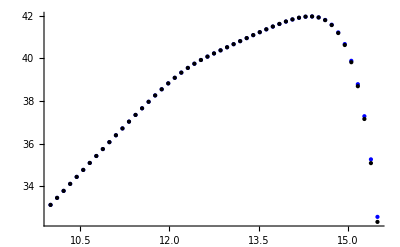

```mathematica
Show[{thindiskPlot,thindiskPlot02}]
```

## SED

Easy way of plotting the SED

```mathematica
LogLogPlot[nu*LnuADAF[nu],{nu,1*^8,1*^21}, PlotRange->{{10*^8.5,10*^19},{10*^35,10*^42}}];
```

I have to use the trick below to be able to compare my computed SED with the data points from Mahadevan's paper. If I want to plot the log of the SED, ParametricPlot simply does not plot with the appropriate range of frequencies so I have to do a change of variables.

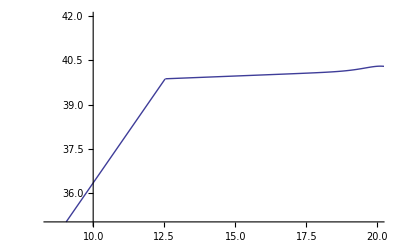

```mathematica
Log[10,nu*LnuADAF] /. nu->10^lognu;
adafplot=Plot[%,{lognu,8,21}, PlotRange->{{8.5,20},{35,42}}]
```

Including all the elements of the model in the plot:

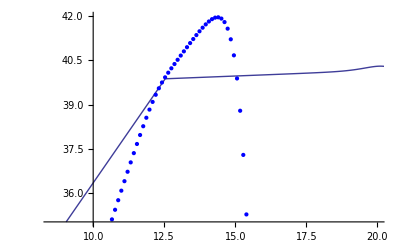

```mathematica
Show[{adafplot,thindiskPlot}]
```

## Comparison with Mahadevan model

```mathematica
(*input="/users/grads/nemmen/Work/doutorado/adaf_code/tests/templates/mahadevan97.csv";
data=Import[input,"Table"];*)
```

```mathematica
(*dataplot=ListPlot[data,PlotStyle->{Red}];*)
```

## Export datafiles

```mathematica
pointsa=100; (*number of points in ADAF SED*)
lognuIa=8.5;
lognuFa=20;
dlognua=(lognuFa-lognuIa)/pointsa;
```

Matrix that gets the SED of the ADAF which will be exported:

```mathematica
nuluma=Table[lognuIa+j*dlognua,{j,0,pointsa},{i,2}];
```

```mathematica
For[j=1,j≤pointsa+1,j++,
nu=10^nuluma[[j,1]];
nuluma[[j,2]]= N[ Log[10,nu*LnuADAF] ];
]
Clear[nu];
```

```mathematica
Export[outadaf,nuluma]
```

simpleadaf.dat